# ICO versus DCO coefficient ratio R scaling with variable N

This standalone notebook studies MSE ≈ c_N/ν for random conjugate displacements α_j=(p_j,0) and β_j=(0,x_j). For each N, it freely fits log(MSE)=a_N log(ν)+b_N as a diagnostic and estimates c_N either with the ν-slope fixed to -1 (recommended) or using the free-fit intercept. It then fits log(c_N) against log(N) for ICO and for the asymptotic DCO lower-bound coefficient. Then the Ratio R between the DCO initial energy and the ICO initial energy when c_N are the same in two cases is plotted.

## Evaluation order

Evaluate all initialization cells first. Then run the quick check or either full study. Here ν denotes the number of shots per Ramsey quadrature. The random seed fixes both the displacement sets and the Monte Carlo samples.

## Core DGW definitions

The following five functions are used: CheckOddDimension, Labels, CanonicalLabel, DGWFourierMatrixXToP, and DGWStateVectorXBasis.

```mathematica
(* ================================================================== *)
(* REUSED FROM THE PREVIOUS NOTEBOOK: "Quantum metrology with ICO.nb" *)
(* The five definitions in this cell have the same mathematical and   *)
(* algorithmic content as in the previous notebook. Only formatting   *)
(* and explanatory comments have been normalized here.                *)
(* ================================================================== *)

ClearAll[
  CheckOddDimension,
  Labels,
  CanonicalLabel,
  DGWFourierMatrixXToP,
  DGWStateVectorXBasis
];

(* FROM PREVIOUS NOTEBOOK; CONTENT UNCHANGED *)
CheckOddDimension[d_Integer] := Module[{},
  If[!OddQ[d] || d <= 0,
    Print["Error: d must be a positive odd integer."];
    Abort[];
  ];
];

(* FROM PREVIOUS NOTEBOOK; CONTENT UNCHANGED *)
Labels[d_Integer] := Module[{m},
  CheckOddDimension[d];
  m = (d - 1)/2;
  Range[-m, m]
];

(* FROM PREVIOUS NOTEBOOK; CONTENT UNCHANGED *)
CanonicalLabel[n_Integer, d_Integer] := Module[{m},
  CheckOddDimension[d];
  m = (d - 1)/2;
  Mod[n + m, d] - m
];

(* FROM PREVIOUS NOTEBOOK; CONTENT UNCHANGED *)
DGWFourierMatrixXToP[d_Integer] := Module[{labels},
  CheckOddDimension[d];
  labels = Labels[d];
  N@Table[Exp[-I 2 Pi n k/d]/Sqrt[d],{k, labels},{n, labels}]
];

(* FROM PREVIOUS NOTEBOOK; CONTENT UNCHANGED *)
DGWStateVectorXBasis[d_Integer,sigma_?NumericQ,x0_?NumericQ,p0_?NumericQ] := 
Module[{m, labels, support, psi,nCanonical, pos, amp, norm},
    CheckOddDimension[d];
    m = (d - 1)/2;
    labels = Labels[d];
    support = Range[Floor[x0] - m, Floor[x0] + m];
    psi = ConstantArray[0. + 0. I, d];
    Do[
      nCanonical = CanonicalLabel[n, d];
      pos = FirstPosition[labels, nCanonical][[1]];
      amp = N[Exp[-Pi (n - x0)^2/sigma^2]* Exp[I 2 Pi p0 (n - x0)/d] ];
      psi[[pos]] += amp,
      {n, support}
    ];
    norm = Sqrt[Conjugate[psi] . psi];
    psi/norm
];
```

## Variable-N simulation and fitting functions

All functions in the next cell aim for the present variable-N studies. In particular, the fast branch propagation, Monte Carlo estimator, random-instance averaging, bias-window selection, and log-log fitting code are not copied from the previous notebook.

```mathematica
(* ================================================================== *)
(* They use the five explicitly labeled DGW definitions imported      *)
(* ================================================================== *)

ClearAll[
  OddDimensionAtLeast,
  DGWScalingCache,
  MakeConjugateScalingInstance,
  FastMSEForScalingInstance,
  AnalyzeScalingInstance,
  FitLogLogData,
  RunVariableNCoefficientStudy,
  RunFixedD65CoefficientStudy,
  RunQuadraticDimensionCoefficientStudy
];

OddDimensionAtLeast[x_?NumericQ] := Module[{d = Ceiling[x]},
  If[OddQ[d], d, d + 1]
];

(* Quantities depending only on d. The memoization avoids rebuilding the
   Fourier matrix and DGW state for every random displacement instance. *)
DGWScalingCache[d_Integer?Positive] /; OddQ[d] :=
  DGWScalingCache[d] = Module[{labels, scale, fourier, psi, q, psiMomentum, energy},
    labels = Labels[d];
    scale = Sqrt[2 Pi/d];
    fourier = DGWFourierMatrixXToP[d];
    psi = DGWStateVectorXBasis[d, N[Sqrt[d]], 0., 0.];
    q = N[scale labels];
    psiMomentum = fourier . psi;
    energy = Chop[Total[Abs[psi]^2 q^2] + Total[Abs[psiMomentum]^2 q^2]];
    <|
      "d" -> d,
      "Labels" -> labels,
      "Scale" -> scale,
      "Fourier" -> fourier,
      "ProbeState" -> psi,
      "QuadratureEigenvalues" -> q,
      "ProbeEnergy" -> N[Re[energy]]
    |>
  ];

(* Exact fast simulation for the conjugate family alpha_j = {p_j,0}, beta_j = {0,x_j}. It propagates the two branch states directly, without constructing a 2d-dimensional controlled-switch matrix. *)

MakeConjugateScalingInstance[d_Integer?Positive,n_Integer?Positive,
pRange:{_?NumericQ, _?NumericQ},xRange:{_?NumericQ, _?NumericQ}
] /; OddQ[d] := 
Module[{cache, fourier, psi, q, energy, pValues, xValues,pTotal, xTotal, phaseAlpha, phaseBeta, applyBeta,branch0, branch1,overlap, pPlusX, pPlusY,pBar, xBar, thetaTarget, gain, omegaReference,omegaFinite, finiteBias, dcoCoefficient},
cache = DGWScalingCache[d];
fourier = cache["Fourier"];
psi = cache["ProbeState"];
q = cache["QuadratureEigenvalues"];
energy = cache["ProbeEnergy"];
pValues = RandomReal[Sort[N[pRange]], n];
xValues = RandomReal[Sort[N[xRange]], n];
pTotal = Total[pValues];
 xTotal = Total[xValues];
phaseAlpha = Exp[I pTotal q];
phaseBeta = Exp[I xTotal q];
applyBeta[v_] := ConjugateTranspose[fourier].(phaseBeta (fourier . v));
(* Branch 0: alpha block followed by beta block. Branch 1: beta block followed by alpha block. *)
branch0 = applyBeta[phaseAlpha psi];
branch1 = phaseAlpha applyBeta[psi];
overlap = Chop[N[Conjugate[branch0] . branch1]];
pPlusX = Clip[N[(1 + Re[overlap])/2], {0., 1.}];
pPlusY = Clip[N[(1 + Im[overlap])/2], {0., 1.}];
pBar = Mean[pValues];
xBar = Mean[xValues];
thetaTarget = pBar xBar;
gain = n^2;
omegaReference = pTotal xTotal;
omegaFinite = -Arg[overlap] + 2 Pi Round[(omegaReference + Arg[overlap])/(2 Pi)];
finiteBias = omegaFinite/gain - thetaTarget;
(* Coefficient of the asymptotic, energy-dependent DCO lower bound: MSE_DCO >= c_DCO(N)/nu. *)
dcoCoefficient = Min[Abs[pBar]^2, Abs[xBar]^2]/(16 energy n^2);
<|
"d" -> d, "N" -> n,"PValues" -> pValues,"XValues" -> xValues,
"PBar" -> pBar,"XBar" -> xBar,"ThetaTarget" -> thetaTarget,
"Gain" -> gain,"OmegaReference" -> omegaReference,"BranchOverlap" -> overlap,
"PPlusX" -> pPlusX,"PPlusY" -> pPlusY,"ProbeEnergy" -> energy,
"FiniteBias" -> finiteBias,
"FiniteBiasSquared" -> finiteBias^2,
"DCOCoefficient" -> dcoCoefficient
|>
  ];

(* Vectorized Monte Carlo estimator.  Here nu is the number of shots in each Ramsey quadrature, matching the convention of the original notebook. *)

FastMSEForScalingInstance[ instance_Association, nu_Integer?Positive, numTrials_Integer?Positive ] := Module[
    {cHat, sHat, zHat, omegaWrapped, omegaUnwrapped,thetaHat, thetaTarget, omegaReference, gain},

    cHat = 2.0 RandomVariate[ BinomialDistribution[nu, instance["PPlusX"]],numTrials]/nu - 1.0;
    sHat = 2.0 RandomVariate[ BinomialDistribution[nu, instance["PPlusY"]],numTrials]/nu - 1.0;
    zHat = cHat + I sHat;
    omegaWrapped = Map[ If[Abs[#] < 10^-14, 0., -Arg[#]] &, zHat];
    omegaReference = instance["OmegaReference"];
    gain = instance["Gain"];
    thetaTarget = instance["ThetaTarget"];
    omegaUnwrapped = omegaWrapped +2 Pi Round[(omegaReference - omegaWrapped)/(2 Pi)];
    thetaHat = omegaUnwrapped/gain;
    Mean[(thetaHat - thetaTarget)^2]
  ];

(* For one random displacement instance, first fit log MSE = a_N log nu + b_N with a free slope.  We also obtain c_N using a fixed slope -1: log MSE = -log nu + log c_N. The largest available nu values that remain above the finite-d bias floor are used. Pearson r, R^2 and log-scale residual diagnostics are returned; |r| below pearsonThreshold raises a warning. *)

AnalyzeScalingInstance::poorfit ="For N=`1` and d=`2`, the log-log MSE fit has |Pearson r|=`3`, below the required threshold `4`.";

AnalyzeScalingInstance[instance_Association,nuList_List,numTrials_Integer?Positive,
biasSafetyFactor_?NumericQ,maxFitPoints_Integer?Positive,pearsonThreshold_ : 0.99]:= Module[
    {mseData, statisticalData, fitData, logFitData,variable, model, expression, nuSlope, nuIntercept,fixedLogCoefficient, xLog, yLog, predictions,residuals, totalVariation, pearsonR, absolutePearsonR,rSquared, freeFitLogRMSE, fixedPredictions,fixedResiduals, fixedSlopeLogRMSE, pearsonPass},
    If[!NumericQ[pearsonThreshold] ||pearsonThreshold < 0 || pearsonThreshold > 1,
      Print["Pearson threshold must lie in [0,1]."];
      Return[$Failed]
    ];
    mseData = Table[{nu, FastMSEForScalingInstance[instance, nu, numTrials]},{nu, nuList}];
    statisticalData = Select[
      mseData,
      #[[2]] > 0 &&
      #[[2]] > biasSafetyFactor instance["FiniteBiasSquared"] &
    ];
    fitData = If[Length[statisticalData] > maxFitPoints,
Take[statisticalData, -maxFitPoints],
statisticalData
];
    If[Length[fitData] < 3,
      Return[
        <|
          "Valid" -> False,
          "MSEData" -> mseData,
          "FitData" -> fitData,
          "Instance" -> instance
        |>
      ]
    ];
    logFitData = ({Log[#[[1]]], Log[#[[2]]]} &) /@ fitData;
    model = LinearModelFit[logFitData, variable, variable];
    expression = Normal[model];
    nuSlope = N[Coefficient[expression, variable]];
    nuIntercept = N[expression /. variable -> 0];
    (* Least-squares intercept in log scale with slope fixed to -1. *)
    fixedLogCoefficient = Mean[(Log[#[[1]]] + Log[#[[2]]]) & /@ fitData];
    xLog = logFitData[[All, 1]];
    yLog = logFitData[[All, 2]];
    pearsonR = N[Correlation[xLog, yLog]];
    absolutePearsonR = If[NumberQ[pearsonR], Abs[pearsonR], Indeterminate];
    predictions = (expression /. variable -> #) & /@ xLog;
    residuals = yLog - predictions;
    totalVariation = Total[(yLog - Mean[yLog])^2];
    rSquared = If[ totalVariation > 0,1 - Total[residuals^2]/totalVariation,Indeterminate];
    freeFitLogRMSE = Sqrt[Mean[residuals^2]];
    fixedPredictions = -xLog + fixedLogCoefficient;
    fixedResiduals = yLog - fixedPredictions;
    fixedSlopeLogRMSE = Sqrt[Mean[fixedResiduals^2]];
    pearsonPass = TrueQ[ NumberQ[pearsonR] && absolutePearsonR >= pearsonThreshold];
    If[!pearsonPass,
      Message[AnalyzeScalingInstance::poorfit,instance["N"],instance["d"],absolutePearsonR,pearsonThreshold]
    ];
    <|
      "Valid" -> True,
      "MSEData" -> mseData,
      "FitData" -> fitData,
      "NuSlope" -> nuSlope,
      "NuExponent" -> -nuSlope,
      "NuFreeIntercept" -> nuIntercept,
      "NuFreeCoefficient" -> Exp[nuIntercept],
      "FixedSlopeLogCoefficient" -> fixedLogCoefficient,
      "FixedSlopeCoefficient" -> Exp[fixedLogCoefficient],
      "PearsonCorrelation" -> pearsonR,
      "AbsolutePearsonCorrelation" -> absolutePearsonR,
      "PearsonThreshold" -> pearsonThreshold,
      "PearsonPass" -> pearsonPass,
      "RSquared" -> rSquared,
      "FreeFitLogRMSE" -> freeFitLogRMSE,
      "FixedSlopeLogRMSE" -> fixedSlopeLogRMSE,
      "DCOCoefficient" -> instance["DCOCoefficient"],
      "FiniteBiasSquared" -> instance["FiniteBiasSquared"],
      "Instance" -> instance
    |>
  ];

FitLogLogData::poorfit ="The fit `1` has |Pearson r|=`2`, below the required threshold `3`.";

FitLogLogData[data_List,fitLabel_String : "log-log data",pearsonThreshold_: 0.99]:= Module[
  {variable, logData, model, expression, slope, intercept,xLog, yLog, predictions, residuals, totalVariation,pearsonR, absolutePearsonR, rSquared, logRMSE, pearsonPass},
  If[!NumericQ[pearsonThreshold] ||pearsonThreshold < 0 || pearsonThreshold > 1,
    Print["Pearson threshold must lie in [0,1]."];
    Return[$Failed]
  ];
  logData = ({Log[#[[1]]], Log[#[[2]]]} &) /@ data;
  model = LinearModelFit[logData, variable, variable];
  expression = Normal[model];
  slope = N[Coefficient[expression, variable]];
  intercept = N[expression /. variable -> 0];
  xLog = logData[[All, 1]];
  yLog = logData[[All, 2]];
  pearsonR = N[Correlation[xLog, yLog]];
  absolutePearsonR =  If[NumberQ[pearsonR], Abs[pearsonR], Indeterminate];
  predictions = (expression /. variable -> #) & /@ xLog;
  residuals = yLog - predictions;
  totalVariation = Total[(yLog - Mean[yLog])^2];
  rSquared = If[ totalVariation > 0, 1 - Total[residuals^2]/totalVariation, Indeterminate ];
  logRMSE = Sqrt[Mean[residuals^2]];
  pearsonPass = TrueQ[ NumberQ[pearsonR] &&   absolutePearsonR >= pearsonThreshold ];
  If[!pearsonPass,
    Message[ FitLogLogData::poorfit, fitLabel, absolutePearsonR,pearsonThreshold]
  ];

  <|
    "FitLabel" -> fitLabel,
    "Slope" -> slope,
    "Intercept" -> intercept,
    "Prefactor" -> Exp[intercept],
    "PearsonCorrelation" -> pearsonR,
    "AbsolutePearsonCorrelation" -> absolutePearsonR,
    "PearsonThreshold" -> pearsonThreshold,
    "PearsonPass" -> pearsonPass,
    "RSquared" -> rSquared,
    "LogFitRMSE" -> logRMSE,
    "Model" -> model
  |>
];



RunVariableNCoefficientStudy[nValues_List,dimensionFunction_,  nuListInput_List,
    numTrials_Integer?Positive,  numInstances_Integer?Positive,randomSeed_Integer,
    pRange : {_?NumericQ, _?NumericQ},xRange : {_?NumericQ, _?NumericQ},
    biasSafetyFactor_?NumericQ, maxFitPoints_Integer?Positive,pearsonThreshold_?NumericQ,
    coefficientMethod_String, fontSize_Integer?Positive, plotTitle_]:= 
Module[
{
nList, nuList, rawResults, summaries, d, instanceResults,validInstances, icoLogs, dcoLogs, slopes, pearsonValues,pearsonPasses, freeFitLogRMSEs, fixedSlopeLogRMSEs,  validSummaries, icoData, dcoData, slopeData, icoFit, dcoFit,points, fittedLines, coefficientPlot, slopePlot, nVariable, nMin, nMax, legend 
},
nList = Sort[DeleteDuplicates[Select[Round[nValues], Positive]]];
nuList = Sort[DeleteDuplicates[Select[Round[nuListInput], Positive]]];
If[!MemberQ[{"FixedNuSlope", "FreeNuSlope"}, coefficientMethod],
Print["Unknown CoefficientMethod: ", coefficientMethod,". Use \"FixedNuSlope\" or \"FreeNuSlope\"."];
Return[$Failed]
];
If[pearsonThreshold < 0 || pearsonThreshold > 1,
Print["Pearson threshold must lie in [0,1]."];
Return[$Failed]
];
rawResults = Table[
d = dimensionFunction[n]; 
If[!IntegerQ[d] || d <= 0 || !OddQ[d],
Print["Invalid dimension d = ", d, " for N = ", n, "."];
Return[$Failed]
];
instanceResults = Table[
BlockRandom[
SeedRandom[randomSeed + 100000 n + instanceIndex];
AnalyzeScalingInstance[MakeConjugateScalingInstance[d, n, pRange, xRange],nuList,numTrials,biasSafetyFactor, maxFitPoints, pearsonThreshold ]
],
{instanceIndex, numInstances}
];
<|"N" -> n,"d" -> d,"Instances" -> instanceResults|>,
{n, nList}
];

summaries = Map[
Function[resultForN,
validInstances = Select[ resultForN["Instances"],TrueQ[#["Valid"]] & ];
If[Length[validInstances] == 0,
(*Then branch, false, nothing to do*)
<|"Valid" -> False, "N" -> resultForN["N"], "d" -> resultForN["d"], "ValidInstances" -> 0|>,
(*Else branch, true, integrate everything*)
icoLogs = Switch[coefficientMethod,
 "FreeNuSlope", (#["NuFreeIntercept"] &) /@ validInstances,
 "FixedNuSlope", (#["FixedSlopeLogCoefficient"] &) /@ validInstances,
 _,{}
];
dcoLogs = Log[(#["DCOCoefficient"] &) /@ validInstances];
slopes = (#["NuSlope"] &) /@ validInstances;
pearsonValues = (#["PearsonCorrelation"] &) /@ validInstances;
pearsonPasses = (#["PearsonPass"] &) /@ validInstances;
freeFitLogRMSEs =(#["FreeFitLogRMSE"] &) /@ validInstances;
fixedSlopeLogRMSEs =(#["FixedSlopeLogRMSE"] &) /@ validInstances;
<|"Valid" -> True,"N" -> resultForN["N"],"d" -> resultForN["d"],
"ValidInstances" -> Length[validInstances],
"ICOCoefficient" -> Exp[Mean[icoLogs]],
"ICOLogCoefficientSE" -> If[Length[icoLogs] > 1, StandardDeviation[icoLogs]/Sqrt[Length[icoLogs]],0.],
"DCOCoefficient" -> Exp[Mean[dcoLogs]],
"DCOLogCoefficientSE" ->If[Length[dcoLogs] > 1, StandardDeviation[dcoLogs]/Sqrt[Length[dcoLogs]], 0.],
"MeanNuSlope" -> Mean[slopes],
"NuSlopeSE" ->If[Length[slopes] > 1,StandardDeviation[slopes]/Sqrt[Length[slopes]],0.],
"MeanNuPearsonCorrelation" -> Mean[pearsonValues],
"MinAbsNuPearsonCorrelation" ->Min[Abs[pearsonValues]],
"AllNuPearsonFitsPass" -> And @@ pearsonPasses,
"MeanFreeFitLogRMSE" -> Mean[freeFitLogRMSEs],
"MeanFixedSlopeLogRMSE" -> Mean[fixedSlopeLogRMSEs]|>
]
],
rawResults
];
validSummaries = Select[summaries,TrueQ[#["Valid"]] &];
If[Length[validSummaries] < 2,
 Print["Fewer than two valid N values remain after bias filtering."];
 Return[<|"SummaryData" -> summaries,"RawResults" -> rawResults|>
]
];
icoData =({#["N"], #["ICOCoefficient"]} &) /@ validSummaries;
dcoData =({#["N"], #["DCOCoefficient"]} &) /@ validSummaries;
slopeData =({#["N"], #["MeanNuSlope"]} &) /@ validSummaries;
icoFit = FitLogLogData[icoData,"ICO coefficient versus N", pearsonThreshold];
dcoFit = FitLogLogData[dcoData,"DCO coefficient versus N",pearsonThreshold];
nMin = Min[icoData[[All, 1]]];
nMax = Max[icoData[[All, 1]]];
points = ListLogLogPlot[{icoData, dcoData},
PlotStyle -> { Directive[Blue, PointSize[0.018]], Directive[Red, PointSize[0.018]]},PlotMarkers -> { {"●", 11}, {"■", 11}  },
Frame -> True,FrameLabel -> {"N", "\!\(\*SubscriptBox[\(c\), \(N\)]\) in MSE ≈ \!\(\*SubscriptBox[\(c\), \(N\)]\)/ν" },
BaseStyle -> {FontSize -> fontSize},PlotRange -> All,ImageSize -> Large, PlotLabel -> plotTitle
];
fittedLines = LogLogPlot[
 Evaluate[{icoFit["Prefactor"] nVariable^icoFit["Slope"],dcoFit["Prefactor"] nVariable^dcoFit["Slope"]}],{nVariable, nMin, nMax},
PlotStyle -> { Directive[Blue, Dashed, Thick], Directive[Red, Dashed, Thick]}
];
legend = LineLegend[
{ Directive[Blue, Thick],Directive[Blue, Dashed, Thick], Directive[Red, Thick],Directive[Red, Dashed, Thick]},
{ 
"ICO Monte Carlo",
Row[{"ICO: slope = ",NumberForm[icoFit["Slope"],{5,3}],", |r| = ",NumberForm[ icoFit["AbsolutePearsonCorrelation"],{5,3}]}],
"DCO asymptotic bound",
Row[{"DCO: slope = ",NumberForm[dcoFit["Slope"], {5,3}],", |r| = ",NumberForm[dcoFit["AbsolutePearsonCorrelation"],{5,3}]}]
},
 LabelStyle -> {FontSize -> Max[12, fontSize - 3]}
];
coefficientPlot = Legended[Show[points, fittedLines, PlotRange -> All],Placed[legend, {0.73, 0.78}]];
slopePlot = ListPlot[slopeData,
Joined -> True,PlotMarkers -> Automatic,PlotStyle -> Directive[Black, Thick],
Frame -> True,FrameLabel -> {"N", "fitted ν-slope \!\(\*SubscriptBox[\(a\), \(N\)]\)"},
GridLines -> {None, {-1}},GridLinesStyle -> Directive[Gray, Dashed],BaseStyle -> {FontSize -> fontSize},
 PlotRange -> All,ImageSize -> Large,PlotLabel -> "Diagnostic: log MSE versus log ν"
];
Print[
"ICO: log(c_N) = ", NumberForm[icoFit["Slope"], {7, 4}], 
" log(N) + ",NumberForm[icoFit["Intercept"], {7, 4}],
"; Pearson r = ",NumberForm[icoFit["PearsonCorrelation"], {7, 5}]
 ];
Print[
"DCO: log(c_N) = ",NumberForm[dcoFit["Slope"], {7, 4}],
" log(N) + ",NumberForm[dcoFit["Intercept"], {7, 4}],
"; Pearson r = ",NumberForm[dcoFit["PearsonCorrelation"], {7, 5}]
];
<|
"CoefficientPlot" -> coefficientPlot,
"NuSlopeDiagnosticPlot" -> slopePlot,
"ICOLogCoefficientFit" -> icoFit,
"DCOLogCoefficientFit" -> dcoFit,
"ICOData" -> icoData,
"DCOData" -> dcoData,
"SummaryData" -> summaries,
"SummaryDataset" -> Dataset[summaries],
"RawResults" -> rawResults,
"NuList" -> nuList,
"NumTrials" -> numTrials,
"NumDisplacementInstances" -> numInstances,
"PearsonThreshold" -> pearsonThreshold,
"CoefficientMethod" -> coefficientMethod,
"RandomSeed" -> randomSeed
|>
];


Options[RunFixedD65CoefficientStudy] = {
  "NValues" -> Range[1, 8],
  "NuList" -> 2^Range[3, 14],
  "NumTrials" -> 20000,
  "NumDisplacementInstances" -> 8,
  "RandomSeed" -> 81192,
  "PRange" -> {0.4, 0.6},
  "XRange" -> {0.4, 0.6},
  "BiasSafetyFactor" -> 5.,
  "MaxFitPoints" -> 6,
  "PearsonThreshold" -> 0.99,
  "CoefficientMethod" -> "FixedNuSlope",
  "FontSize" -> 20
};

RunFixedD65CoefficientStudy[OptionsPattern[]]:=
  RunVariableNCoefficientStudy[
    OptionValue["NValues"],
    Function[{n}, 65],
    OptionValue["NuList"],
    OptionValue["NumTrials"],
    OptionValue["NumDisplacementInstances"],
    OptionValue["RandomSeed"],
    OptionValue["PRange"],
    OptionValue["XRange"],
    OptionValue["BiasSafetyFactor"],
    OptionValue["MaxFitPoints"],
    OptionValue["PearsonThreshold"],
    OptionValue["CoefficientMethod"],
    OptionValue["FontSize"],
    "Fixed dimension d = 65"
  ];

Options[RunQuadraticDimensionCoefficientStudy] = {
  "NValues" -> Range[1, 16],
  "DimensionPrefactor" -> 1.,
  "NuList" -> 2^Range[3, 14],
  "NumTrials" -> 20000,
  "NumDisplacementInstances" -> 8,
  "RandomSeed" -> 81192,
  "PRange" -> {0.4, 0.6},
  "XRange" -> {0.4, 0.6},
  "BiasSafetyFactor" -> 5.,
  "MaxFitPoints" -> 6,
  "PearsonThreshold" -> 0.99,
  "CoefficientMethod" -> "FixedNuSlope",
  "FontSize" -> 20
};

RunQuadraticDimensionCoefficientStudy[OptionsPattern[]] := Module[
  {dimensionPrefactor = OptionValue["DimensionPrefactor"]},

  RunVariableNCoefficientStudy[
    OptionValue["NValues"],
    Function[
      {n},
      OddDimensionAtLeast[dimensionPrefactor n^2 + 1]
    ],
    OptionValue["NuList"],
    OptionValue["NumTrials"],
    OptionValue["NumDisplacementInstances"],
    OptionValue["RandomSeed"],
    OptionValue["PRange"],
    OptionValue["XRange"],
    OptionValue["BiasSafetyFactor"],
    OptionValue["MaxFitPoints"],
    OptionValue["PearsonThreshold"],
    OptionValue["CoefficientMethod"],
    OptionValue["FontSize"],
    Row[{
      "Quadratic dimension: d ≈ ",
      dimensionPrefactor,
      " N^2"
    }]
  ]
];
```

## Replot completed results without rerunning

The following function uses only the ICO data, DCO data, fitted models, and summaries already stored in a completed result association. Changing its label or style options does not repeat the Monte Carlo simulation.

```mathematica
(* NEW: redraw a completed study without repeating any Monte Carlo work.
   This function only reads data already stored in the result association. *)

ClearAll[PlotVariableNCoefficientStudy];

PlotVariableNCoefficientStudy::missing =
  "The supplied result association is missing the required keys `1`.";

Options[PlotVariableNCoefficientStudy] = {
  "CoefficientFrameLabel" -> {
    "N",
    "\!\(\*SubscriptBox[\(c\), \(N\)]\) in MSE ≈ \
\!\(\*SubscriptBox[\(c\), \(N\)]\)/ν"
  },
  "SlopeFrameLabel" -> {
    "N",
    "fitted ν-slope \!\(\*SubscriptBox[\(a\), \(N\)]\)"
  },
  "CoefficientPlotLabel" -> None,
  "SlopePlotLabel" -> "Diagnostic: log MSE versus log ν",
  "ICOLegendLabel" -> "ICO Monte Carlo",
  "DCOLegendLabel" -> "DCO asymptotic bound",
  "ICOFitLegendPrefix" -> "ICO fit",
  "DCOFitLegendPrefix" -> "DCO fit",
  "LegendPosition" -> {0.73, 0.78},
  "FontSize" -> 20,
  "ImageSize" -> Large
};

PlotVariableNCoefficientStudy[result_Association, OptionsPattern[]]:= Module[
{requiredKeys, missingKeys, icoData, dcoData, validSummaries,slopeData, icoFit, dcoFit, nVariable, nMin, nMax,points,fittedLines,legend,coefficientPlot,slopePlot,legendFontSize,icoPointSample,dcoPointSample,icoLineSample,dcoLineSample },
requiredKeys = {
"ICOData",
"DCOData",
"SummaryData",
"ICOLogCoefficientFit",
"DCOLogCoefficientFit"
};
missingKeys = Select[requiredKeys, MissingQ[Lookup[result, #]] & ];
If[missingKeys =!= {},
Message[PlotVariableNCoefficientStudy::missing, missingKeys];
Return[$Failed]
];
icoData = result["ICOData"];
dcoData = result["DCOData"];
icoFit = result["ICOLogCoefficientFit"];
dcoFit = result["DCOLogCoefficientFit"];
validSummaries = Select[result["SummaryData"],AssociationQ[#] && TrueQ[Lookup[#, "Valid", False]] &];
slopeData =({#["N"], #["MeanNuSlope"]} &) /@ validSummaries;
nMin = Min[icoData[[All, 1]]];
nMax = Max[icoData[[All, 1]]];
points = ListLogLogPlot[{icoData, dcoData},
PlotStyle -> {Directive[Blue, PointSize[0.018]],Directive[Red, PointSize[0.018]]},
PlotMarkers -> {{"●", 11},{"■", 11}},
Frame -> True,
FrameLabel -> OptionValue["CoefficientFrameLabel"],
BaseStyle -> {FontSize -> OptionValue["FontSize"]},
PlotRange -> All,
ImageSize -> OptionValue["ImageSize"],
PlotLabel -> OptionValue["CoefficientPlotLabel"]
];
fittedLines = LogLogPlot[
Evaluate[{icoFit["Prefactor"] nVariable^icoFit["Slope"],dcoFit["Prefactor"] nVariable^dcoFit["Slope"]}],{nVariable, nMin, nMax},
PlotStyle -> { Directive[Blue, Dashed, Thick], Directive[Red, Dashed, Thick]}
];
legendFontSize=Max[12,OptionValue["FontSize"]-3];
icoPointSample=Graphics[{Inset[Style["●",Blue,12],{0.5,0.5}]},PlotRange->{{0,1},{0,1}},ImageSize->{38,15},AspectRatio->15/38,ImagePadding->0];
dcoPointSample=Graphics[{Inset[Style["■",Red,12],{0.5,0.5}]},PlotRange->{{0,1},{0,1}},ImageSize->{38,15},AspectRatio->15/38,ImagePadding->0];
icoLineSample=Graphics[{Directive[Blue,Dashed,AbsoluteThickness[2]],Line[{{0.05,0.5},{0.95,0.5}}]},PlotRange->{{0,1},{0,1}},ImageSize->{38,15},AspectRatio->15/38,ImagePadding->0];
dcoLineSample=Graphics[{Directive[Red,Dashed,AbsoluteThickness[2]],Line[{{0.05,0.5},{0.95,0.5}}]},PlotRange->{{0,1},{0,1}},ImageSize->{38,15},AspectRatio->15/38,ImagePadding->0];
legend=Grid[
{
{icoPointSample,Style[OptionValue["ICOLegendLabel"],FontSize->legendFontSize]},
{icoLineSample,Style[Row[{OptionValue["ICOFitLegendPrefix"]}],FontSize->legendFontSize]},(*{icoLineSample,Style[Row[{OptionValue["ICOFitLegendPrefix"],": slope = ",NumberForm[icoFit["Slope"],{5,3}],", |r| = ",NumberForm[icoFit["AbsolutePearsonCorrelation"],{5,3}]}],FontSize->legendFontSize]},*){dcoPointSample,Style[OptionValue["DCOLegendLabel"],FontSize->legendFontSize]},{dcoLineSample,Style[Row[{OptionValue["DCOFitLegendPrefix"]}],FontSize->legendFontSize]}
(*{dcoLineSample,Style[Row[{OptionValue["DCOFitLegendPrefix"],": slope = ",NumberForm[dcoFit["Slope"],{5,3}],", |r| = ",NumberForm[dcoFit["AbsolutePearsonCorrelation"],{5,3}]}],FontSize->legendFontSize]}*)
},
Alignment->{{Center,Left},Center},Spacings->{0.5,0.25}
];
coefficientPlot = Legended[Show[points, fittedLines, PlotRange -> All],Placed[legend, OptionValue["LegendPosition"]]];
slopePlot = ListPlot[slopeData,
Joined -> True,PlotMarkers -> Automatic,  PlotStyle -> Directive[Black, Thick],
Frame -> True,FrameLabel -> OptionValue["SlopeFrameLabel"],
GridLines -> {None, {-1}}, GridLinesStyle -> Directive[Gray, Dashed],
BaseStyle -> {FontSize -> OptionValue["FontSize"]},PlotRange -> All,
ImageSize -> OptionValue["ImageSize"],PlotLabel -> OptionValue["SlopePlotLabel"]
];
<|"CoefficientPlot" -> coefficientPlot,"NuSlopeDiagnosticPlot" -> slopePlot|>
];
```

## Energy-ratio post-processing

ComputeInitialEnergyRatioStudy and PlotInitialEnergyRatioStudy reuse DGWScalingCache and FitLogLogData unchanged, do not rerun the Monte Carlo simulation, evaluate the ICO probe energy directly, solve the DCO Cramer-Rao coefficient for the energy required to match the fitted ICO coefficient, and retain an algebraic coefficient-ratio check. The plot uses logarithmic axes for both N and R, showing only the R data, its fitted power law, and a horizontal dashed R = 1 reference line.

```mathematica
(* ================================================================ *)
(* NEW IN THIS REVISION: initial-energy ratio R versus N            *)
(* Reuses DGWScalingCache and FitLogLogData from the notebook.      *)
(* ================================================================ *)
ClearAll[ComputeInitialEnergyRatioStudy,PlotInitialEnergyRatioStudy];

ComputeInitialEnergyRatioStudy::missing="The input association must contain SummaryData and RawResults from a completed variable-N study.";

ComputeInitialEnergyRatioStudy::few="Fewer than two valid positive data points are available for the energy-ratio fit.";

Options[ComputeInitialEnergyRatioStudy]={"DCORepetitionsPerNotebookNu"->1};

ComputeInitialEnergyRatioStudy[result_Association,OptionsPattern[]]:=Module[
{requiredRowKeys,validSummaries,ratioSummaries,ratioData,ratioFit,pearsonThreshold,dcoShotMultiplier,rawResults},
(*Validate input association*)
If[!AllTrue[{"SummaryData","RawResults"},KeyExistsQ[result,#]&],
Message[ComputeInitialEnergyRatioStudy::missing];
Return[$Failed]
];
dcoShotMultiplier=OptionValue["DCORepetitionsPerNotebookNu"];
If[!NumericQ[dcoShotMultiplier]||dcoShotMultiplier<=0,
Return[$Failed]
];
rawResults=result["RawResults"];
requiredRowKeys={"N","d","ICOCoefficient","DCOCoefficient"};
(*Select valid summary rows*)validSummaries=Select[result["SummaryData"],Function[row,TrueQ[Lookup[row,"Valid",False]]&&AllTrue[requiredRowKeys,KeyExistsQ[row,#]&]&&IntegerQ[row["d"]]&&OddQ[row["d"]]&&row["d"]>0&&AllTrue[Lookup[row,{"ICOCoefficient","DCOCoefficient"}],NumericQ[#]&&TrueQ[#>0]&]]
];
(*Build ratio summaries*)
ratioSummaries=Map[
Function[row,
Module[{n,d,cICO,cDCOAtEICO,eICO,dcoCRNumerator,eDCOMatching,energyRatio,rawForN,validInstanceAnalyses,instances,dcoCRNumerators},
n=row["N"];
d=row["d"];
cICO=row["ICOCoefficient"];
cDCOAtEICO=row["DCOCoefficient"];
rawForN=SelectFirst[rawResults,#1["N"]===n&,Missing["NotAvailable"]];
validInstanceAnalyses=Select[rawForN["Instances"],TrueQ[Lookup[#1,"Valid",False]]&];
instances=(#1["Instance"]&)/@validInstanceAnalyses;
(*Direct evaluation of<X^2+P^2>for the DGW probe*)
eICO=N[Re[DGWScalingCache[d]["ProbeEnergy"]]];
(*Compute K_N directly from the same valid displacement instances.For each instance,c_DCO(E)=K_i/E with K_i=Min[Abs[pBar]^2,Abs[xBar]^2]/(16 N^2).*)dcoCRNumerators=(Min[Abs[#1["PBar"]]^2,Abs[#1["XBar"]]^2]/(16 n^2)&)/@instances;
dcoCRNumerator=Exp[Mean[Log[dcoCRNumerators]]];
(*Allocate the fitted ICO coefficient c_N,then solve K_N/(s E_DCO)=c_N for the CR-implied DCO energy.*)eDCOMatching=dcoCRNumerator/(dcoShotMultiplier cICO);
energyRatio=eDCOMatching/eICO;
<|
"N"->n,"d"->d,"ICOCoefficient"->cICO,"DCOCoefficientAtICOEnergy"->cDCOAtEICO,
"ICOProbeEnergy"->eICO,"DCOCRNumerator"->dcoCRNumerator,"CRImpliedDCOEnergy"->eDCOMatching,
"InitialEnergyRatio"->energyRatio,"CoefficientRatioCheck"->cDCOAtEICO/(dcoShotMultiplier cICO)
|>
]
],
validSummaries
];
ratioData=({#["N"],#["InitialEnergyRatio"]}&)/@ratioSummaries;
If[Length[ratioData]<2,
Message[ComputeInitialEnergyRatioStudy::few];
Return[$Failed]
];
pearsonThreshold=Lookup[result,"PearsonThreshold",0.99];
ratioFit=FitLogLogData[ratioData,"DCO/ICO initial-energy ratio versus N",pearsonThreshold];
<|
"EnergyRatioData"->ratioData,"EnergyRatioFit"->ratioFit,
"EnergyRatioSummaryData"->ratioSummaries,
"EnergyRatioDataset"->Dataset[ratioSummaries],
"DCORepetitionsPerNotebookNu"->dcoShotMultiplier
|>
];

PlotInitialEnergyRatioStudy::missing="Run ComputeInitialEnergyRatioStudy first and pass its output to this function.";

Options[PlotInitialEnergyRatioStudy]={"FrameLabel"->{"N","Required initial-energy ratio  R"},"PlotLabel"->None,"FontSize"->22,"ImageSize"->Large,"LegendPosition"->{0.72,0.25}};
PlotInitialEnergyRatioStudy[study_Association,OptionsPattern[]]:=Module[
{ratioData,ratioFit,nMin,nMax,nVariable,points,fittedLine,unityLine,legend,plot},If[!AllTrue[{"EnergyRatioData","EnergyRatioFit"},KeyExistsQ[study,#]&],Message[PlotInitialEnergyRatioStudy::missing];
Return[$Failed]
];
ratioData=study["EnergyRatioData"];
ratioFit=study["EnergyRatioFit"];
nMin=Min[ratioData[[All,1]]];
nMax=Max[ratioData[[All,1]]];
points=ListLogLogPlot[ratioData,PlotStyle->Directive[Blue,PointSize[0.018]],PlotMarkers->{{"●",11}},Joined->False,Frame->True,FrameLabel->OptionValue["FrameLabel"],BaseStyle->{FontSize->OptionValue["FontSize"]},PlotRange->All,ImageSize->OptionValue["ImageSize"],PlotLabel->OptionValue["PlotLabel"]];
fittedLine=LogLogPlot[Evaluate[ratioFit["Prefactor"] nVariable^ratioFit["Slope"]],{nVariable,nMin,nMax},PlotStyle->Directive[Blue,Thick],Axes->False];
unityLine=LogLogPlot[1,{nVariable,nMin,nMax},PlotStyle->Directive[GrayLevel[0.45],Dashed,Thick],Axes->False];
legend=Grid[
{
{PointLegend[{Directive[Blue,PointSize[0.018]]},{"Energy ratio"},LabelStyle->{FontSize->Max[12,OptionValue["FontSize"]-3]}]},{LineLegend[{Directive[Blue,Thick],Directive[GrayLevel[0.45],Dashed,Thick]},{"Energy ratio fit","R = 1"},LabelStyle->{FontSize->Max[12,OptionValue["FontSize"]-3]}]}
},
Alignment->{{Center,Left},Center},Spacings->{0.5,0.25}];
plot=Legended[Show[points,fittedLine,unityLine,PlotRange->All],Placed[legend,OptionValue["LegendPosition"]]];
Print["Energy ratio: log(R) = ",NumberForm[ratioFit["Slope"],{7,4}]," log(N) + ",NumberForm[ratioFit["Intercept"],{7,4}],"; Pearson r = ",NumberForm[ratioFit["PearsonCorrelation"],{7,5}]];
plot
];
```

## Quick check

This small run checks that all definitions evaluate and that the plots are produced before starting the longer studies.

ICO: log(c_N) = -4.3569 log(N) + -0.1911; Pearson r = -0.99918

DCO: log(c_N) = -1.8032 log(N) + -4.4654; Pearson r = -0.99988

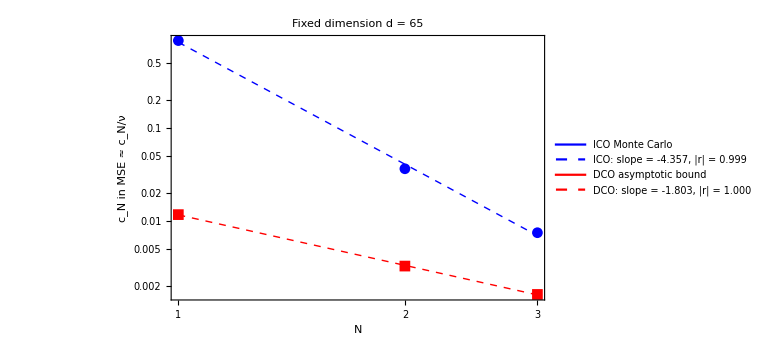

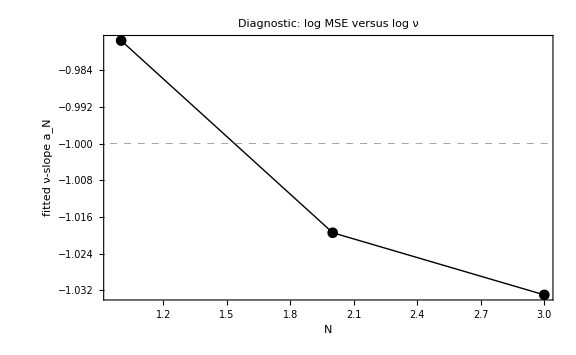

```mathematica
quickResult = RunFixedD65CoefficientStudy[
  "NValues" -> Range[1, 3],
  "NuList" -> 2^Range[3, 9],
  "NumTrials" -> 1000,
  "NumDisplacementInstances" -> 2,
  "PearsonThreshold" -> 0.99,
  "RandomSeed" -> 81192
];

quickResult["CoefficientPlot"]
quickResult["NuSlopeDiagnosticPlot"]
quickResult["SummaryDataset"]
```

## Study 1: fixed d=65 and N=1,…,8

With p_j,x_j∈[0.4,0.6], the sufficient bulk condition gives (8/π)(0.6)^2 N^2≈0.9167 N^2≤65 for N≤8.

ICO: log(c_N) = -4.0075 log(N) + -0.3987; Pearson r = -0.99753

DCO: log(c_N) = -1.9197 log(N) + -4.3694; Pearson r = -0.99970

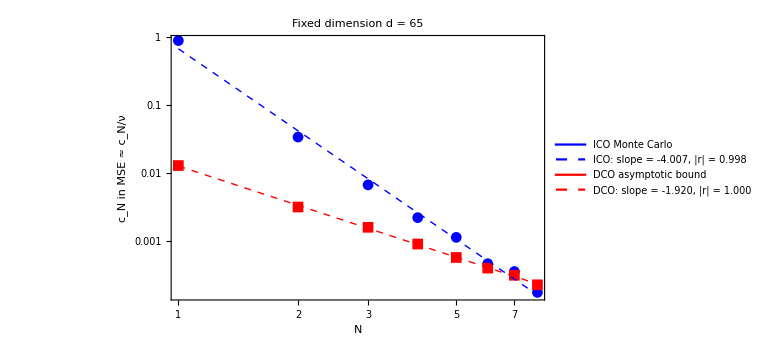

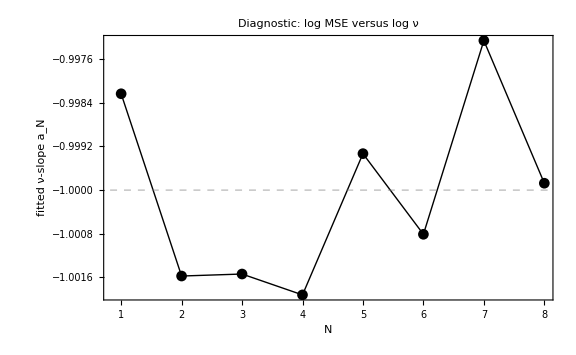

```mathematica
fixedResult = RunFixedD65CoefficientStudy[
  "NValues" -> Range[1, 8],
  "PRange" -> {0.4, 0.6},
  "XRange" -> {0.4, 0.6},
  "PearsonThreshold" -> 0.99,
  "RandomSeed" -> 81192
];

fixedResult["CoefficientPlot"]
fixedResult["NuSlopeDiagnosticPlot"]
fixedResult["SummaryDataset"]
```

## Study 2: d≈N.b2 and N=1,…,16

The DGW construction requires odd d. The function therefore uses the smallest odd integer not below N.b2+1: d=N.b2+1 for even N and d=N.b2+2 for odd N. The ranges [0.4,0.6] make dimension prefactor 1 sufficient under the stated bulk bound.

ICO: log(c_N) = -3.9800 log(N) + -0.3916; Pearson r = -0.99887

DCO: log(c_N) = -1.9526 log(N) + -4.3055; Pearson r = -0.99974

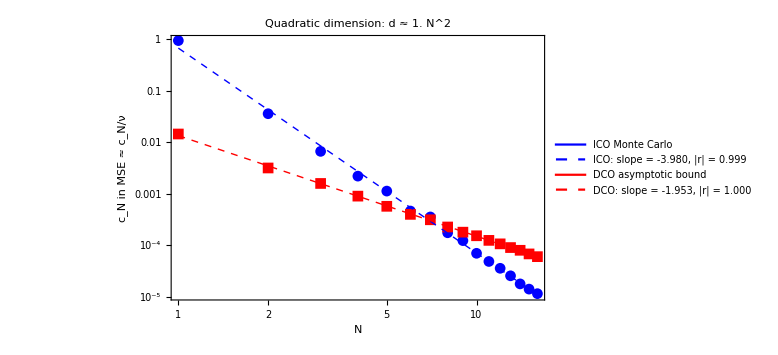

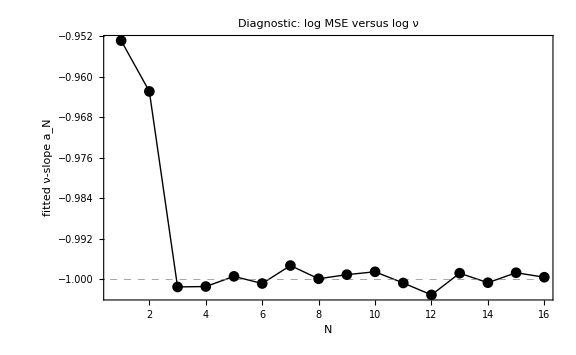

```mathematica
quadraticResult = RunQuadraticDimensionCoefficientStudy[
  "NValues" -> Range[1, 16],
  "DimensionPrefactor" -> 1.,
  "PRange" -> {0.4, 0.6},
  "XRange" -> {0.4, 0.6},
  "PearsonThreshold" -> 0.99,
  "RandomSeed" -> 81192
];

quadraticResult["CoefficientPlot"]
quadraticResult["NuSlopeDiagnosticPlot"]
quadraticResult["SummaryDataset"]
```

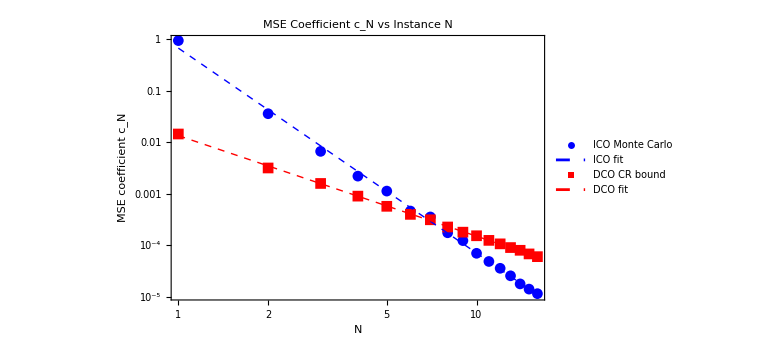

```mathematica
study2Plots=PlotVariableNCoefficientStudy[quadraticResult,"CoefficientFrameLabel"->{"N","MSE coefficient \!\(\*SubscriptBox[\(c\), \(N\)]\)"},
"CoefficientPlotLabel"->"MSE Coefficient \!\(\*SubscriptBox[\(c\), \(N\)]\) vs Instance \!\(N\) ",
"SlopeFrameLabel"->{"N","fitted exponent with respect to ν"},
"SlopePlotLabel"->"ICO scaling with ν",
"ICOLegendLabel"->"ICO Monte Carlo",
"DCOLegendLabel"->"DCO CR bound",
"LegendPosition"->{0.73,0.80},
"FontSize"->22
];


study2Plots["CoefficientPlot"]
```

## Initial-energy ratio R versus N

This is post-processing of the same d approximately N^2 data used in the current coefficient figure. For every N, the code evaluates E_ICO directly, writes the DCO Cramer-Rao coefficient as K_N/E_DCO, and solves K_N/E_DCO = c_N^ICO. The resulting R points are fitted directly on log-log axes. The equal-energy value R = 1 is drawn only as a horizontal dashed reference line, not as a second dataset. Thus the plotted R is a CR-implied necessary energy ratio, not the achieved energy of a constructed optimal DCO protocol. The value 1 below follows the notebook's literal per-quadrature coefficient convention; change it to 2 only if DCO is assigned the same total 2 nu physical shots used by the two ICO Ramsey quadratures.

Energy ratio: log(R) = 2.0274 log(N) + -3.9139; Pearson r = 0.99658

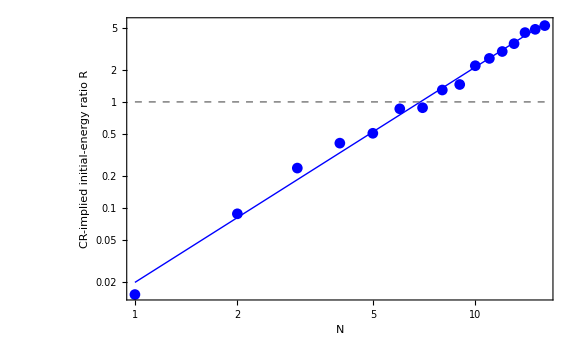

```mathematica
(* Apply the energy-ratio post-processing to the completed d approximately N^2 study underlying the current Fig. 3.
   Multiplier 1 implements the literal coefficient equality in this notebook. *)
energyRatioResult = ComputeInitialEnergyRatioStudy[quadraticResult,"DCORepetitionsPerNotebookNu" -> 1];

energyRatioPlot = PlotInitialEnergyRatioStudy[energyRatioResult,
"FrameLabel" -> {"N", "CR-implied initial-energy ratio R"},
"PlotLabel" -> None,
"FontSize" -> 22,
"LegendPosition" -> {0.72, 0.25}
];

energyRatioPlot
energyRatioResult["EnergyRatioDataset"]
```

## Higher-accuracy run

This run is substantially slower. Use it after inspecting the quick and default results.

ICO: log(c_N) = -4.0087 log(N) + -0.3175; Pearson r = -0.99928

DCO: log(c_N) = -1.9724 log(N) + -4.2596; Pearson r = -0.99985

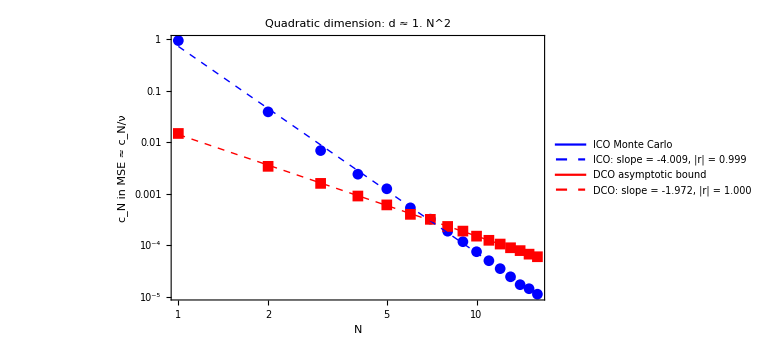

```mathematica
accurateQuadraticResult =
  RunQuadraticDimensionCoefficientStudy[
    "NValues" -> Range[1, 16],
    "DimensionPrefactor" -> 1.,
    "PRange" -> {0.4, 0.6},
    "XRange" -> {0.4, 0.6},
    "NuList" -> 2^Range[3, 14],
    "NumTrials" -> 50000,
    "NumDisplacementInstances" -> 20,
    "PearsonThreshold" -> 0.99,
    "RandomSeed" -> 81192
  ];

accurateQuadraticResult["CoefficientPlot"]
```

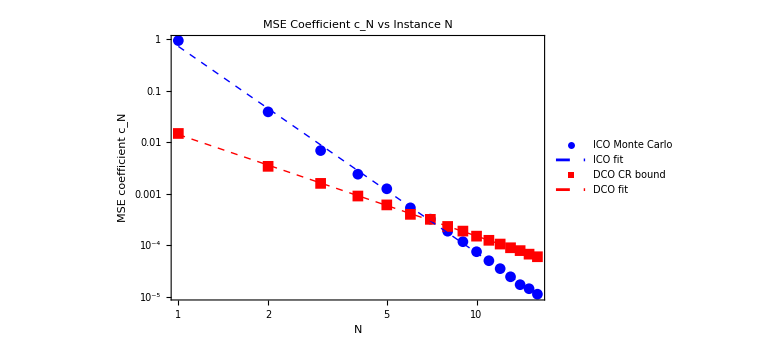

```mathematica
higherAccuracyPlots=PlotVariableNCoefficientStudy[accurateQuadraticResult,"CoefficientFrameLabel"->{"N","MSE coefficient \!\(\*SubscriptBox[\(c\), \(N\)]\)"},
"CoefficientPlotLabel"->"MSE Coefficient \!\(\*SubscriptBox[\(c\), \(N\)]\) vs Instance \!\(N\) ",
"SlopeFrameLabel"->{"N","fitted exponent with respect to ν"},
"SlopePlotLabel"->"ICO scaling with ν",
"ICOLegendLabel"->"ICO Monte Carlo",
"DCOLegendLabel"->"DCO CR bound",
"LegendPosition"->{0.73,0.80},
"FontSize"->22
];

higherAccuracyPlots["CoefficientPlot"]
```

## Initial-energy ratio R versus N

This is post-processing of the same d approximately N^2 data used in the current coefficient figure. For every N, the code evaluates E_ICO directly, writes the DCO Cramer-Rao coefficient as K_N/E_DCO, and solves K_N/E_DCO = c_N^ICO. The resulting R points are fitted directly on log-log axes. The equal-energy value R = 1 is drawn only as a horizontal dashed reference line, not as a second dataset. Thus the plotted R is a CR-implied necessary energy ratio, not the achieved energy of a constructed optimal DCO protocol. The value 1 below follows the notebook's literal per-quadrature coefficient convention; change it to 2 only if DCO is assigned the same total 2 nu physical shots used by the two ICO Ramsey quadratures.

Energy ratio: log(R) = 2.0363 log(N) + -3.9421; Pearson r = 0.99797

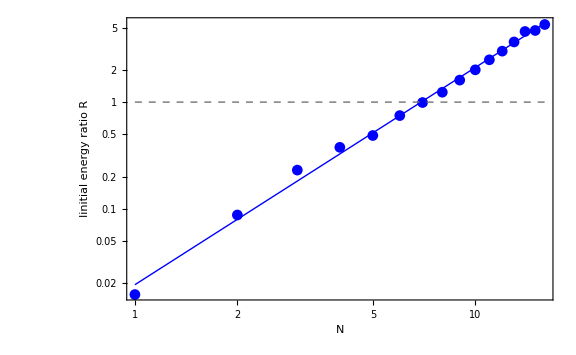

```mathematica
(* Apply the energy-ratio post-processing to the completed d approximately N^2 study underlying the current Fig. 3.
   Multiplier 1 implements the literal coefficient equality in this notebook. *)
accuracyEnergyRatioResult = ComputeInitialEnergyRatioStudy[accurateQuadraticResult,"DCORepetitionsPerNotebookNu" -> 1];

accuracyEnergyRatioPlot = PlotInitialEnergyRatioStudy[accuracyEnergyRatioResult,
"FrameLabel" -> {"N", "Iinitial energy ratio R"},
"PlotLabel" -> None,
"FontSize" -> 22,
"LegendPosition" -> {0.72, 0.25}
];

accuracyEnergyRatioPlot
accuracyEnergyRatioResult["EnergyRatioDataset"]
```

## Cache reset

```mathematica
(* Run this only after changing a definition used by the cached
   d-dependent DGW data. *)
(*Clear[DGWScalingCache];*)
```